```mathematica
NN = 1000
Λ = 10
2.0 Log[Λ/m0]
Λ^2
cc[k_]  :=  Exp[ (ⅈ 2 π k)/NN]
circ= Array[cc, NN, 0];
Needs["PlotLegends`"]
```

1000

10

2. Log[10/m0]

100

```mathematica
funcsum[s_] := 1/NN∑_(k=0)^(NN-1) (s - circ[[k+1]]) Log [ s - circ[[k+1]]]
```

```mathematica
funcanalyt0[s_] := ( - π s + ⅈ ( s - 1 ) )
```

```mathematica
funcanalyt[s_] := s Log [ s ]
```

```mathematica
funcanalyt2[s_] := 1/NN s Log [ s^NN ]
```

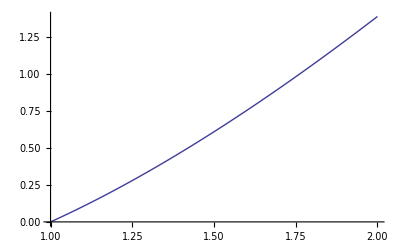

```mathematica
Plot[{Re[funcsum[s]]}, {s,1.0, 2.0}]
```

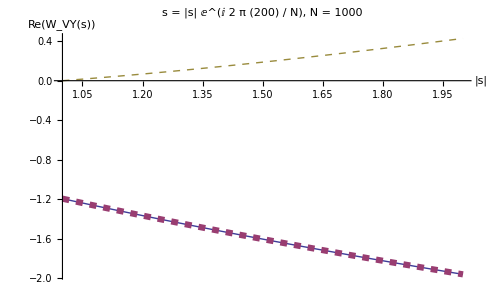

```mathematica
Plot[{Re[funcsum[s ⅇ^(ⅈ 2 π (200) / NN)]], Re[funcanalyt[s ⅇ^(ⅈ 2 π (200) / NN)]],  Re[funcanalyt2[ s ⅇ^(ⅈ 2 π (200) / NN)]]}, {s,1.0, 2.0}, 
PlotStyle->{Thick,{Thickness[0.009],Dashed},{Thick,Dashed}}, PlotLabel->Style["s = |s| ⅇ^(ⅈ 2 π (200) / N), N = 1000", FontSize->20],
AxesLabel->{Style["|s|", FontSize->20],Style["Re(W_VY(s))", FontSize->20]}]
```

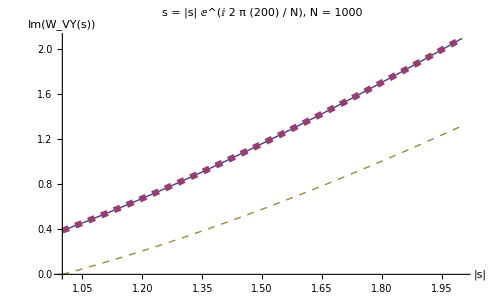

```mathematica
Plot[{Im[funcsum[s ⅇ^(ⅈ 2 π (200) / NN)]], Im[funcanalyt[s ⅇ^(ⅈ 2 π (200) / NN)]],  Im[funcanalyt2[ s ⅇ^(ⅈ 2 π (200) / NN)]]}, {s,1.0, 2.0}, 
PlotStyle->{Thick,{Thickness[0.009],Dashed},{Thick,Dashed}}, PlotLabel->Style["s = |s| ⅇ^(ⅈ 2 π (200) / N), N = 1000", FontSize->20],
AxesLabel->{Style["|s|", FontSize->20],Style["Im(W_VY(s))", FontSize->20]}]
```

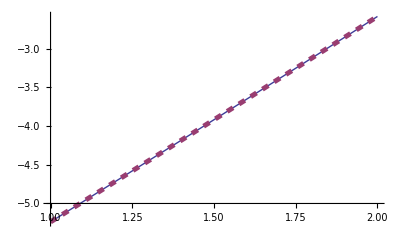

```mathematica
Plot[{Re[funcsum[s+5.ⅈ]], Re[funcanalyt[s+5.ⅈ]]}, {s,1.0, 2.0}, PlotStyle->{Thick,{Thickness[0.009],Dashed}}]
```

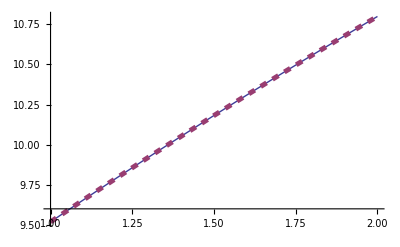

```mathematica
Plot[{Im[funcsum[s+5.ⅈ]], Im[funcanalyt[s+5.ⅈ]]},{s,1.0, 2.0}, PlotStyle->{Thick,{Thickness[0.009],Dashed}}]
```

```mathematica
funcsum[0] // N
```

-1.-0.000314159 ⅈ

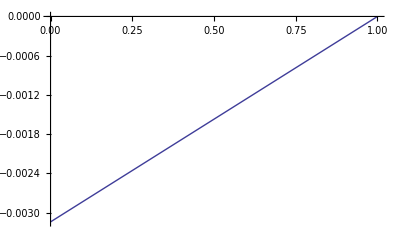

```mathematica
Plot[{Im[funcsum[s]]}, {s,0.,1.0}]
```